```mathematica
prob2= {
x>=-4/5&&x<=-1/3&&y<=3/2&&y≥1, 
{{-x+a*x(x^2+y^2),x+a*y(x^2+y^2)}/.{a->1},{x,y}, True},
x>-1/3||x*y<0||2 y>1||x^3<-4/5
};

prob= {
(x1-3/2)^2+x2^2≤1/4, 
{{x2,-x1 + x1^3/3-x2},{x1,x2}, True},
Not[(x1+1)^2+(x2+1)^2≤0.16]
}
```

{(-3/2+x1)^2+x2^2≤1/4,{{x2,-x1+x1^3/3-x2},{x1,x2},True},(1+x1)^2+(1+x2)^2>0.16}

```mathematica
B=BarrierCertificateMethod`BarrierCertificate[prob, NPrecision->3]
```

OpenMATLAB::wspo: The MATLAB workspace is already open.

MScript::owrt: An MScript by that name already exists. Use "Overwrite" -> True to overwrite.

-1779/1250-(501 x1)/400-(32329 x1^2)/100000-(18857 x2)/10000-(2681 x1 x2)/3125-8.7833×10^-7 x2^2

```mathematica
B=-1779/1250-(501 x1)/400-(32329 x1^2)/100000-(18857 x2)/10000-(2681 x1 x2)/3125-8.7833*^-7 x2^2
```

-1779/1250-(501 x1)/400-(32329 x1^2)/100000-(18857 x2)/10000-(2681 x1 x2)/3125-8.7833×10^-7 x2^2

{x2,-x1+x1^3/3-x2}

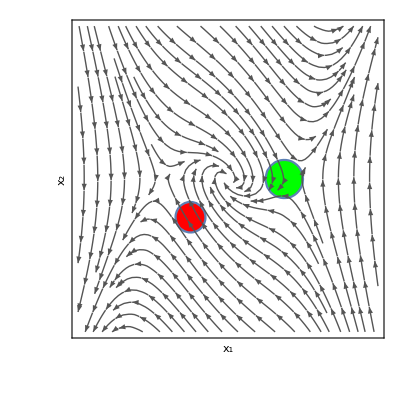

```mathematica
{x1min, x1max} = {-4, 4};
    {x2min, x2max} = {-4, 4};
    prob[[2]][[1]]
    Show[
      RegionPlot[prob[[1]], {x1, x1min, x1max}, {x2, x2min, x2max}, PlotStyle -> Green, FrameStyle->Large, FrameTicks->None, FrameLabel->{Subscript[x, 1],Subscript[x, 2]}, PlotRangePadding->None] ,(* Plot initial states in green *)
      RegionPlot[Not[prob[[3]]], {x1, x1min, x1max}, {x2, x2min, x2max}, PlotStyle->Red], (* Plot invariant *) 
     StreamPlot[prob[[2]][[1]], {x1, x1min, x1max}, {x2, x2min, x2max}, StreamStyle -> Darker[Gray]] (* Plot vector field *)

      ]
```